```mathematica
SetDirectory[NotebookDirectory[]];
```

## Unvariate

```mathematica
fAR[ρ_,σ_,n_]:=(Normal@RandomFunction[ARProcess[{ρ},σ],{n}])[[1]]
```

```mathematica
cols=ColorData[97,"ColorList"];
```

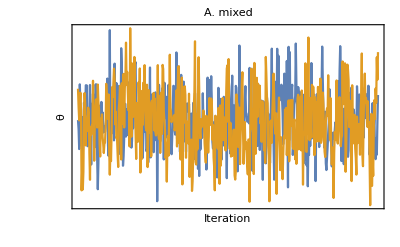

```mathematica
n=500;
chain1=fAR[0.25, 1, n];
chain2=fAR[0.25, 1, n]; 
dist1=SmoothKernelDistribution[chain1[[All,2]]];
dist2=SmoothKernelDistribution[chain2[[All,2]]];
g1=ListLinePlot[{chain1, chain2},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{30,80},{20,10}},
Epilog->{{{cols[[1]],Line[Table[{n+20+300PDF[dist1,x],x},{x,-3,3,0.01}]]}},{{cols[[2]],Line[Table[{n+20+300PDF[dist2,x],x},{x,-3,3,0.01}]]}}},FrameTicks->None,Frame->{True,True,False,False},Axes->False,FrameLabel->{"Iteration","θ"},LabelStyle->{FontSize->16,Black},FrameStyle->Black,PlotLabel->"A. mixed"]
```

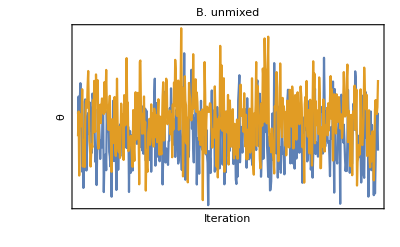

```mathematica
chain1=fAR[0.25, 1, n];
temp=fAR[0.25, 1, n];
chain2=Thread[{temp[[All,1]],temp[[All,2]]+0.5}]; 
dist1=SmoothKernelDistribution[chain1[[All,2]]];
dist2=SmoothKernelDistribution[chain2[[All,2]]];
g2=ListLinePlot[{chain1, chain2},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{30,80},{20,10}},
Epilog->{{{cols[[1]],Line[Table[{n+20+300PDF[dist1,x],x},{x,-3,3,0.01}]]}},{{cols[[2]],Line[Table[{n+20+300PDF[dist2,x],x},{x,-3,3,0.01}]]}}},FrameTicks->None,Frame->{True,True,False,False},Axes->False,FrameLabel->{"Iteration","θ"},LabelStyle->{FontSize->16,Black},FrameStyle->Black,PlotLabel->"B. unmixed"]
```

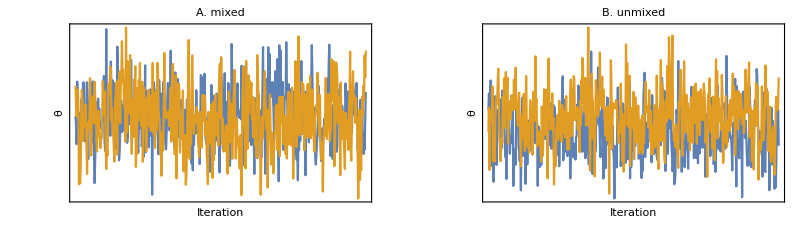

```mathematica
gFinal=GraphicsRow[{g1,g2},ImageSize->800]
```

```mathematica
Export["../output/unmixed_1.pdf",gFinal]
```

../output/unmixed_1.pdf

## Multivariate

```mathematica
fSimple[x_,y_]:=PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}]
fCorrelated[x_,y_]:=PDF[MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}],{x,y}]
```

```mathematica
fStep[x_,y_,σ_]:=RandomVariate[MultinormalDistribution[{0,0},{{σ,0},{0,σ}}],1][[1]]
fStepAccept[x_,y_,f_,σ_]:=Block[{proposed=fStep[x,y,σ]},If[f[proposed[[1]],proposed[[2]]]/f[x,y]>RandomReal[],proposed,{x,y}]]
fMCMC[numiter_Integer,f_,σ_]:=NestList[fStepAccept[#[[1]],#[[2]],f,σ]&,RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],1][[1]],numiter]
```

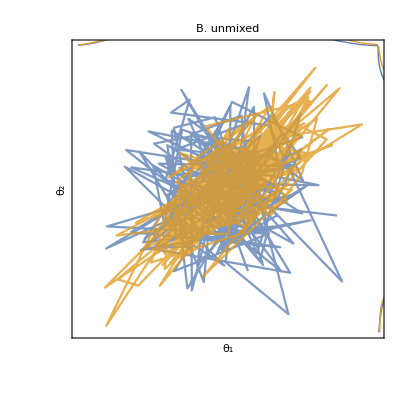

```mathematica
samples1=RandomVariate[MultinormalDistribution[{0,0},{{1,0.0},{0.0,1}}],200];
samples2=RandomVariate[MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}],200];
dist11=SmoothKernelDistribution[samples1[[All,1]]];
dist12=SmoothKernelDistribution[samples1[[All,2]]];
dist21=SmoothKernelDistribution[samples2[[All,1]]];
dist22=SmoothKernelDistribution[samples2[[All,2]]];
mult=3;
g3=ListLinePlot[{samples1, samples2},PlotStyle->{Opacity[0.8,cols[[1]]],Opacity[0.8,cols[[2]]]},PlotRange->{{-mult,mult},{-mult,mult}},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{30,90},{25,90}},Axes->False,Frame->True,FrameTicks->None,AspectRatio->1,Epilog->{{cols[[1]],Line[Table[{mult+5PDF[dist12,x],x},{x,-mult,mult,0.01}]]},{cols[[2]],Line[Table[{mult+5PDF[dist22,x],x},{x,-mult,mult,0.01}]]},{cols[[1]],Line[Table[{x,mult+5PDF[dist11,x]},{x,-mult,mult,0.01}]]},{cols[[2]],Line[Table[{x,mult+5PDF[dist21,x]},{x,-mult,mult,0.01}]]}},FrameStyle->Black,FrameLabel->{"θ_1","θ_2"},LabelStyle->{FontSize->16,Black},PlotLabel->"B. unmixed"]
```

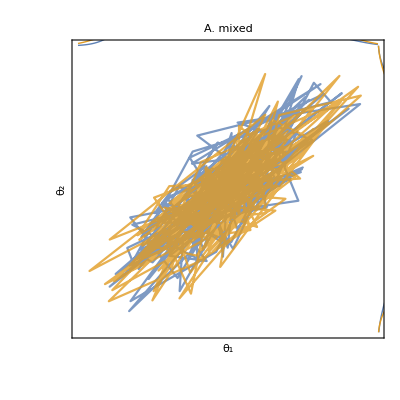

```mathematica
samples1=RandomVariate[MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}],200];
samples2=RandomVariate[MultinormalDistribution[{0,0},{{1,0.8},{0.8,1}}],200];
dist11=SmoothKernelDistribution[samples1[[All,1]]];
dist12=SmoothKernelDistribution[samples1[[All,2]]];
dist21=SmoothKernelDistribution[samples2[[All,1]]];
dist22=SmoothKernelDistribution[samples2[[All,2]]];
mult=3;
g4=ListLinePlot[{samples1, samples2},PlotStyle->{Opacity[0.8,cols[[1]]],Opacity[0.8,cols[[2]]]},PlotRange->{{-mult,mult},{-mult,mult}},PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{30,90},{25,90}},Axes->False,Frame->True,FrameTicks->None,AspectRatio->1,Epilog->{{cols[[1]],Line[Table[{mult+5PDF[dist12,x],x},{x,-mult,mult,0.01}]]},{cols[[2]],Line[Table[{mult+5PDF[dist22,x],x},{x,-mult,mult,0.01}]]},{cols[[1]],Line[Table[{x,mult+5PDF[dist11,x]},{x,-mult,mult,0.01}]]},{cols[[2]],Line[Table[{x,mult+5PDF[dist21,x]},{x,-mult,mult,0.01}]]}},FrameStyle->Black,FrameLabel->{"θ_1","θ_2"},LabelStyle->{FontSize->16,Black},PlotLabel->"A. mixed"]
```

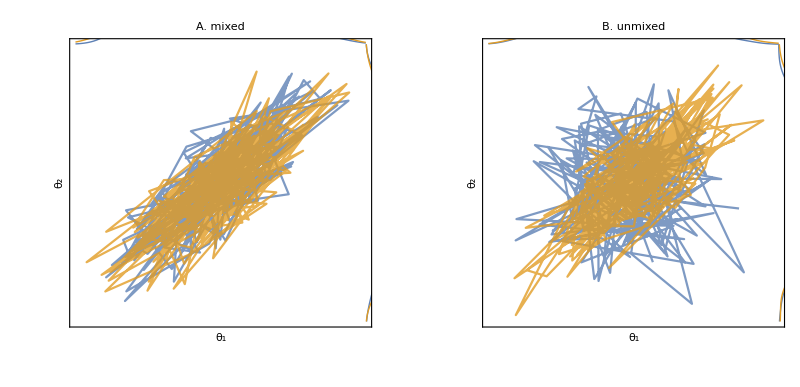

```mathematica
gFinal1=GraphicsRow[{g4,g3},ImageSize->800]
```

```mathematica
Export["../output/unmixed_2.pdf",gFinal1]
```

../output/unmixed_2.pdf